```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"RABBIT_Packages"}]];
Needs["MagicMap`"]
myParallelNeeds["MagicMap`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\DirectoryWUR\RABBIT Software\RABBIT_Example Scripts

```mathematica
?magicMap
```

magicMap[magicsnp, model, popdesign,ngroup]performs linage map construction in multi-parental populations. The magicsnp specifies the input genotypic data matrix or filename. The model specifies whether the maternally and paternally derived chromosomes are indepdent ("indepModel"), completely dependent ("depModel"), or  modeled jointly ("jointModel"). The popdesign specifies the breeding design information in several possible ways: a list of mating schemes from founder population to the last generation, a list of values denoting the junction distribution, or a filename for population  pedigree information. The ngroup specifies the number of linkage groups.

```mathematica
dataid="Example"
magicsnpfile=dataid<>"_ObservedGenotype.csv"
model="jointModel";
popdesignfile=dataid<>"_PedigreeInfor.csv"
ngroup=5
```

Example

Example_ObservedGenotype.csv

Example_PedigreeInfor.csv

5

```mathematica
(*take every second marker. set thin =1 using all markers*)
thin=2;
```

```mathematica
magicsnp=Import[magicsnpfile];
(*thinning markers to reduce demonstration time*)
magicsnp=getsubMagicSNP[magicsnp,All,;;;;thin];
magicsnp[[2;;10,;;10]]//MatrixForm
refmapfile=Export[dataid<>"_refmap.csv",Transpose[magicsnp[[2;;4]]]]
magicsnp[[3;;4,2;;]]="NA";
```

(marker | MN1_29291 | MN1_112907 | MN1_197787 | MN1_444820 | MN1_592863 | BKN118 | CRY2_1021 | AXR1_381 | MN1_1602026
chromosome | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
pos(cM) | 0.14646 | 0.56454 | 0.98894 | 2.22383 | 2.96434 | 3.80793 | 5.93921 | 7.50114 | 8.01014
Founder1 | 1 | 2 | 1 | 1 | 1 | N | 2 | N | 2
Founder2 | N | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 1
Founder3 | 2 | N | 2 | 2 | 1 | 2 | 1 | 1 | 1
Founder4 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 1
ProgenyLine1 | 11 | NN | 11 | 11 | 11 | 22 | 11 | 21 | 11
ProgenyLine2 | 22 | 11 | 22 | 22 | 11 | 22 | 11 | 11 | 11)

Example_refmap.csv

```mathematica
Options[magicMap]
```

{founderAllelicError→0.005,offspringAllelicError→0.005,isFounderInbred→True,computingLodType→both,sequenceDataOption→{isFounderAllelicDepth→Automatic,isOffspringAllelicDepth→Automatic,minPhredQualScore→30,priorFounderCallThreshold→0.99},outputFileID→,isPrintTimeElapsed→True,isRunInParallel→True,minLodSaving→1,miniComponentSize→5,graphLaplacian→rwNormalized,eigenVectorSelection→eigenratio,nConnectedComponent→1,lodTypeClustering→both,lodTypeOrdering→both,minLodClustering→Automatic,minLodOrdering→Automatic,nNeighborFunction→(√#1&),nNeighborSaving→10,referenceMap→None,delStrongCrossLink→True,isImputingFounder→True,detectingThreshold→0.9,imputingThreshold→1,nReplicateAnnealing→1,initTemperature→2,coolingRate→0.85,freezingTemperature→0.5,deltLoglThreshold→1,MaxIterations→50}

--------------------------------------------------Calculate PairwiseFraction----------------------------------------------------------

magicPairwiseSimilarity. Start date = Thu 30 Aug 2018 16:15:03. Outputfile = Example_pairwiseSimilarity.txt

{#founder, #offspring, #SNP} ={4,100,389}

model is set to "depModel" since the IBD probability = 0.875(>0.85)!

Done! Finished date =Thu 30 Aug 2018 16:15:44. 	Time elapsed in total = 41. Seconds.

-----------------------------------------------------Construct LinkageMap-------------------------------------------------------------

magicMapConstruct. Start date = Thu 30 Aug 2018 16:15:44. Outputfile = Example_initialLinkageMap.csv

Size of 3 connected componets: {387,1,1}; dropping components with size <= 5!

The option value of minLodClustering is set to 2.248!

Size of groups = {86,69,70,71,91} and #ungrouped markers = 2 after spectral clustering!Time elapsed in total = 2.8 Seconds.

The option value of minLodOrderingng is set to {2.248, 2.248, 2.248, 2.248, 2.248}!

# NearestNeighbors = {10,9,9,9,10}

ratios between eigenvalues[[5;;]]: {1.5167,2.73382,1.41158,3.96872,1.94988}; peak={2,4}

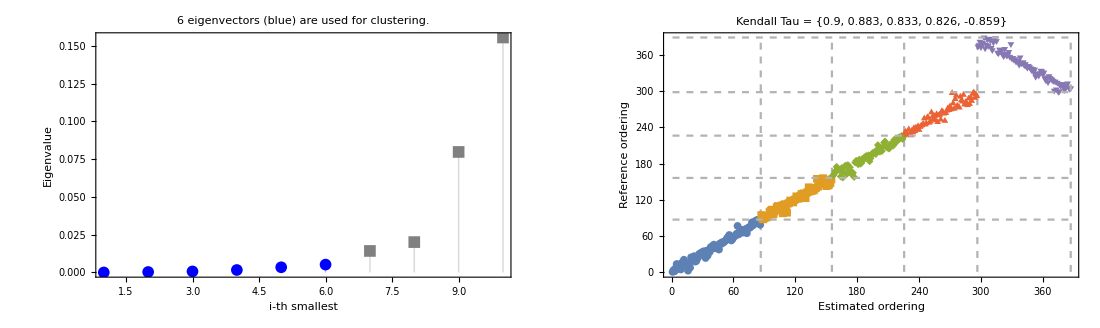

Genetic map function for initial map construction: scaled fraction = 1-Exp[-2.75 distance(M)]

Done! Finished date =Thu 30 Aug 2018 16:15:48. 	Time elapsed in total = 4.1 Seconds.

-------------------------------------------------------Refine LinkageMap-------------------------------------------------------------

magicMapRefine. Start date = Thu 30 Aug 2018 16:15:48. Outputfiles = {Example_refiningHistory.txt,Example_refinedLinkageMap.csv,Example_refinedMagicSNP.csv}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={1,2,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={4,1.22825,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={7,0.754299,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={10,0.463234,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={11,0.284484,True,True,False}

{Iteration,Temperature,ParentImpute&Phasing,ErrorDetect,OffspringImpute}={16,0.0248508,True,True,False}

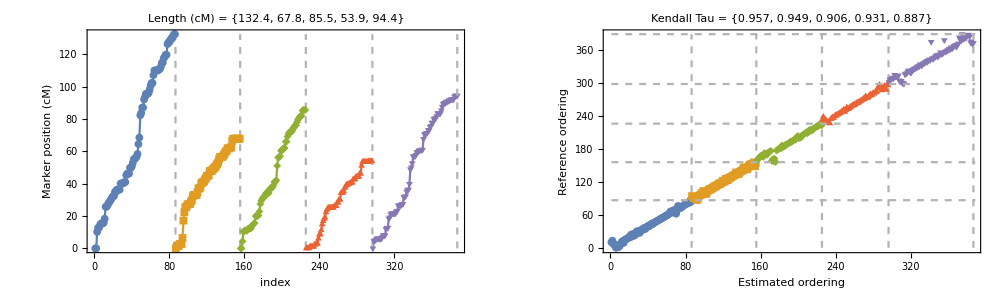

# iterations = {{20},{20},{20},{25},{20}}

Done! Finished date =Thu 30 Aug 2018 16:23:56. 	Time elapsed in total = 487.8 Seconds.

------------------------------------------------------------End---------------------------------------------------------------------

{533.139,Null}

{Example_pairwiseSimilarity.txt,Example_initialLinkageMap.csv,{Example_refiningHistory.txt,Example_refinedLinkageMap.csv,Example_refinedMagicSNP.csv}}

```mathematica
(*refmapfile is used only for monitoring the iterative improvement of genetic map*)
outputfiles=magicMap[magicsnp,model,popdesignfile,ngroup,referenceMap->refmapfile,outputFileID->dataid];//AbsoluteTiming
outputfiles
```